```mathematica
Clear[Aαi,AαiC,AαiA,AαiAC,α,Dαi,DαiC]
Aαi=AαiA+ϕ Dαi;
AαiC=AαiAC+ϕ DαiC;
Print[Style[" α Aαi Aαi^* term:",Red,16]]
fα=Expand[α Aαi AαiC]
```

α Aαi Aαi^* term:

AαiA AαiAC α+AαiAC Dαi α ϕ+AαiA DαiC α ϕ+Dαi DαiC α ϕ^2

```mathematica
Clear[Aαi,Aβj,Aβj1,Aβj2,AαiC1,AαiC2,α,β1,AαiA,AβjA,AαiAC,Dβj,Dαi,Dαi,DαiC]
Aαi=AαiA+ϕ Dαi;
(*************)
Aβj1=AβjA+ϕ Dβj;
Aβj2=AβjA+ϕ Dβj;
AαiC1=AαiAC+ϕ DαiC;
AαiC2=AαiAC+ϕ DαiC;
Print[Style[" β1 Aαi^* Aαi^* Aβj Aβj term:",Red,16]]
fβ1=Expand[β1 AαiC1 AαiC2 Aβj1 Aβj2]
```

β1 Aαi^* Aαi^* Aβj Aβj term:

AαiAC^2 AβjA^2 β1+2 AαiAC AβjA^2 DαiC β1 ϕ+2 AαiAC^2 AβjA Dβj β1 ϕ+AβjA^2 DαiC^2 β1 ϕ^2+4 AαiAC AβjA DαiC Dβj β1 ϕ^2+AαiAC^2 Dβj^2 β1 ϕ^2+2 AβjA DαiC^2 Dβj β1 ϕ^3+2 AαiAC DαiC Dβj^2 β1 ϕ^3+DαiC^2 Dβj^2 β1 ϕ^4

```mathematica
Clear[Aαi,Aβj,Aβj1,Aβj2,AαiC,AαiC1,AβjC,AαiC2,α,β1,β2,AαiA,AβjA,AαiAC,AβjAC,Dβj,Dαi,Dαi,DαiC,DβjC]
Aαi=AαiA+ϕ Dαi;
Aβj=AβjA+ϕ Dβj;
AαiC=AαiAC+ϕ DαiC;
AβjC=AβjAC+ϕ DβjC;
Print[Style[" β2 Aαi^* Aαi Aβj^* Aβj term:",Red,16]]
fβ2=Expand[β2 AαiC Aαi AβjC Aβj]
```

β2 Aαi^* Aαi Aβj^* Aβj term:

AαiA AαiAC AβjA AβjAC β2+AαiAC AβjA AβjAC Dαi β2 ϕ+AαiA AβjA AβjAC DαiC β2 ϕ+AαiA AαiAC AβjAC Dβj β2 ϕ+AαiA AαiAC AβjA DβjC β2 ϕ+AβjA AβjAC Dαi DαiC β2 ϕ^2+AαiAC AβjAC Dαi Dβj β2 ϕ^2+AαiA AβjAC DαiC Dβj β2 ϕ^2+AαiAC AβjA Dαi DβjC β2 ϕ^2+AαiA AβjA DαiC DβjC β2 ϕ^2+AαiA AαiAC Dβj DβjC β2 ϕ^2+AβjAC Dαi DαiC Dβj β2 ϕ^3+AβjA Dαi DαiC DβjC β2 ϕ^3+AαiAC Dαi Dβj DβjC β2 ϕ^3+AαiA DαiC Dβj DβjC β2 ϕ^3+Dαi DαiC Dβj DβjC β2 ϕ^4

```mathematica
Clear[Aαi,Aβj,Aβj1,Aβj2,AαiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,AαiA,AβjA,AαiAC,AβjAC,Dβj,Dαi,Dαi,DαiC,DβjC]
Aαi=AαiA+ϕ Dαi;
Aαj=AαjA+ϕ Dαj;
Aβj=AβjA+ϕ Dβj;
AαiC=AαiAC+ϕ DαiC;
AβjC=AβjAC+ϕ DβjC;
AβiC=AβiAC+ϕ DβiC;
Print[Style[" β3 Aαi^* Aβi^* Aαj Aβj term:",Red,16]]
fβ3=Expand[β3 AαiC AβiC Aαj Aβj]
```

β3 Aαi^* Aβi^* Aαj Aβj term:

AαiAC AαjA AβiAC AβjA β3+AαjA AβiAC AβjA DαiC β3 ϕ+AαiAC AβiAC AβjA Dαj β3 ϕ+AαiAC AαjA AβjA DβiC β3 ϕ+AαiAC AαjA AβiAC Dβj β3 ϕ+AβiAC AβjA DαiC Dαj β3 ϕ^2+AαjA AβjA DαiC DβiC β3 ϕ^2+AαiAC AβjA Dαj DβiC β3 ϕ^2+AαjA AβiAC DαiC Dβj β3 ϕ^2+AαiAC AβiAC Dαj Dβj β3 ϕ^2+AαiAC AαjA DβiC Dβj β3 ϕ^2+AβjA DαiC Dαj DβiC β3 ϕ^3+AβiAC DαiC Dαj Dβj β3 ϕ^3+AαjA DαiC DβiC Dβj β3 ϕ^3+AαiAC Dαj DβiC Dβj β3 ϕ^3+DαiC Dαj DβiC Dβj β3 ϕ^4

```mathematica
Clear[Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,AαiA,AαjA,AβiA,AβjA,AαiAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,Dαi,DβjC,DαiC,DβiC,DβjC]
Aαi=AαiA+ϕ Dαi;
Aβi=AβiA+ϕ Dβi;
Aαj=AαjA+ϕ Dαj;
Aβj=AβjA+ϕ Dβj;
AαiC=AαiAC+ϕ DαiC;
AβjC=AβjAC+ϕ DβjC;
AβiC=AβiAC+ϕ DβiC;
Print[Style[" β4 Aαi^* Aβi Aβj^* Aαj term:",Red,16]]
fβ4=Expand[β4 AαiC Aβi AβjC Aαj]
```

β4 Aαi^* Aβi Aβj^* Aαj term:

AαiAC AαjA AβiA AβjAC β4+AαjA AβiA AβjAC DαiC β4 ϕ+AαiAC AβiA AβjAC Dαj β4 ϕ+AαiAC AαjA AβjAC Dβi β4 ϕ+AαiAC AαjA AβiA DβjC β4 ϕ+AβiA AβjAC DαiC Dαj β4 ϕ^2+AαjA AβjAC DαiC Dβi β4 ϕ^2+AαiAC AβjAC Dαj Dβi β4 ϕ^2+AαjA AβiA DαiC DβjC β4 ϕ^2+AαiAC AβiA Dαj DβjC β4 ϕ^2+AαiAC AαjA Dβi DβjC β4 ϕ^2+AβjAC DαiC Dαj Dβi β4 ϕ^3+AβiA DαiC Dαj DβjC β4 ϕ^3+AαjA DαiC Dβi DβjC β4 ϕ^3+AαiAC Dαj Dβi DβjC β4 ϕ^3+DαiC Dαj Dβi DβjC β4 ϕ^4

```mathematica
Clear[Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC]
Aαi=AαiA+ϕ Dαi;
Aβi=AβiA+ϕ Dβi;
Aαj=AαjA+ϕ Dαj;
Aβj=AβjA+ϕ Dβj;
AαiC=AαiAC+ϕ DαiC;
AαjC=AαjAC+ϕ DαjC;
AβjC=AβjAC+ϕ DβjC;
AβiC=AβiAC+ϕ DβiC;
Print[Style[" β5 Aαi^* Aβi Aβj Aαj^* term:",Red,16]]
fβ5=Expand[β5 AαiC Aβi Aβj AαjC]
```

β5 Aαi^* Aβi Aβj Aαj^* term:

AαiAC AαjAC AβiA AβjA β5+AαjAC AβiA AβjA DαiC β5 ϕ+AαiAC AβiA AβjA DαjC β5 ϕ+AαiAC AαjAC AβjA Dβi β5 ϕ+AαiAC AαjAC AβiA Dβj β5 ϕ+AβiA AβjA DαiC DαjC β5 ϕ^2+AαjAC AβjA DαiC Dβi β5 ϕ^2+AαiAC AβjA DαjC Dβi β5 ϕ^2+AαjAC AβiA DαiC Dβj β5 ϕ^2+AαiAC AβiA DαjC Dβj β5 ϕ^2+AαiAC AαjAC Dβi Dβj β5 ϕ^2+AβjA DαiC DαjC Dβi β5 ϕ^3+AβiA DαiC DαjC Dβj β5 ϕ^3+AαjAC DαiC Dβi Dβj β5 ϕ^3+AαiAC DαjC Dβi Dβj β5 ϕ^3+DαiC DαjC Dβi Dβj β5 ϕ^4

AαiA AαiAC α+AαiAC^2 AβjA^2 β1+AαiA AαiAC AβjA AβjAC β2+AαiAC AαjA AβiAC AβjA β3+AαiAC AαjA AβiA AβjAC β4+AαiAC AαjAC AβiA AβjA β5+AαiAC Dαi α ϕ+AαiA DαiC α ϕ+2 AαiAC AβjA^2 DαiC β1 ϕ+2 AαiAC^2 AβjA Dβj β1 ϕ+AαiAC AβjA AβjAC Dαi β2 ϕ+AαiA AβjA AβjAC DαiC β2 ϕ+AαiA AαiAC AβjAC Dβj β2 ϕ+AαiA AαiAC AβjA DβjC β2 ϕ+AαjA AβiAC AβjA DαiC β3 ϕ+AαiAC AβiAC AβjA Dαj β3 ϕ+AαiAC AαjA AβjA DβiC β3 ϕ+AαiAC AαjA AβiAC Dβj β3 ϕ+AαjA AβiA AβjAC DαiC β4 ϕ+AαiAC AβiA AβjAC Dαj β4 ϕ+AαiAC AαjA AβjAC Dβi β4 ϕ+AαiAC AαjA AβiA DβjC β4 ϕ+AαjAC AβiA AβjA DαiC β5 ϕ+AαiAC AβiA AβjA DαjC β5 ϕ+AαiAC AαjAC AβjA Dβi β5 ϕ+AαiAC AαjAC AβiA Dβj β5 ϕ+Dαi DαiC α ϕ^2+AβjA^2 DαiC^2 β1 ϕ^2+4 AαiAC AβjA DαiC Dβj β1 ϕ^2+AαiAC^2 Dβj^2 β1 ϕ^2+AβjA AβjAC Dαi DαiC β2 ϕ^2+AαiAC AβjAC Dαi Dβj β2 ϕ^2+AαiA AβjAC DαiC Dβj β2 ϕ^2+AαiAC AβjA Dαi DβjC β2 ϕ^2+AαiA AβjA DαiC DβjC β2 ϕ^2+AαiA AαiAC Dβj DβjC β2 ϕ^2+AβiAC AβjA DαiC Dαj β3 ϕ^2+AαjA AβjA DαiC DβiC β3 ϕ^2+AαiAC AβjA Dαj DβiC β3 ϕ^2+AαjA AβiAC DαiC Dβj β3 ϕ^2+AαiAC AβiAC Dαj Dβj β3 ϕ^2+AαiAC AαjA DβiC Dβj β3 ϕ^2+AβiA AβjAC DαiC Dαj β4 ϕ^2+AαjA AβjAC DαiC Dβi β4 ϕ^2+AαiAC AβjAC Dαj Dβi β4 ϕ^2+AαjA AβiA DαiC DβjC β4 ϕ^2+AαiAC AβiA Dαj DβjC β4 ϕ^2+AαiAC AαjA Dβi DβjC β4 ϕ^2+AβiA AβjA DαiC DαjC β5 ϕ^2+AαjAC AβjA DαiC Dβi β5 ϕ^2+AαiAC AβjA DαjC Dβi β5 ϕ^2+AαjAC AβiA DαiC Dβj β5 ϕ^2+AαiAC AβiA DαjC Dβj β5 ϕ^2+AαiAC AαjAC Dβi Dβj β5 ϕ^2+2 AβjA DαiC^2 Dβj β1 ϕ^3+2 AαiAC DαiC Dβj^2 β1 ϕ^3+AβjAC Dαi DαiC Dβj β2 ϕ^3+AβjA Dαi DαiC DβjC β2 ϕ^3+AαiAC Dαi Dβj DβjC β2 ϕ^3+AαiA DαiC Dβj DβjC β2 ϕ^3+AβjA DαiC Dαj DβiC β3 ϕ^3+AβiAC DαiC Dαj Dβj β3 ϕ^3+AαjA DαiC DβiC Dβj β3 ϕ^3+AαiAC Dαj DβiC Dβj β3 ϕ^3+AβjAC DαiC Dαj Dβi β4 ϕ^3+AβiA DαiC Dαj DβjC β4 ϕ^3+AαjA DαiC Dβi DβjC β4 ϕ^3+AαiAC Dαj Dβi DβjC β4 ϕ^3+AβjA DαiC DαjC Dβi β5 ϕ^3+AβiA DαiC DαjC Dβj β5 ϕ^3+AαjAC DαiC Dβi Dβj β5 ϕ^3+AαiAC DαjC Dβi Dβj β5 ϕ^3+DαiC^2 Dβj^2 β1 ϕ^4+Dαi DαiC Dβj DβjC β2 ϕ^4+DαiC Dαj DβiC Dβj β3 ϕ^4+DαiC Dαj Dβi DβjC β4 ϕ^4+DαiC DαjC Dβi Dβj β5 ϕ^4

AαiA AαiAC α+AαiAC^2 AβjA^2 β1+AαiA AαiAC AβjA AβjAC β2+AαiAC AαjA AβiAC AβjA β3+AαiAC AαjA AβiA AβjAC β4+AαiAC AαjAC AβiA AβjA β5+(AαiAC Dαi α+AαiA DαiC α+2 AαiAC AβjA^2 DαiC β1+2 AαiAC^2 AβjA Dβj β1+AαiAC AβjA AβjAC Dαi β2+AαiA AβjA AβjAC DαiC β2+AαiA AαiAC AβjAC Dβj β2+AαiA AαiAC AβjA DβjC β2+AαjA AβiAC AβjA DαiC β3+AαiAC AβiAC AβjA Dαj β3+AαiAC AαjA AβjA DβiC β3+AαiAC AαjA AβiAC Dβj β3+AαjA AβiA AβjAC DαiC β4+AαiAC AβiA AβjAC Dαj β4+AαiAC AαjA AβjAC Dβi β4+AαiAC AαjA AβiA DβjC β4+AαjAC AβiA AβjA DαiC β5+AαiAC AβiA AβjA DαjC β5+AαiAC AαjAC AβjA Dβi β5+AαiAC AαjAC AβiA Dβj β5) ϕ+(Dαi DαiC α+AβjA^2 DαiC^2 β1+4 AαiAC AβjA DαiC Dβj β1+AαiAC^2 Dβj^2 β1+AβjA AβjAC Dαi DαiC β2+AαiAC AβjAC Dαi Dβj β2+AαiA AβjAC DαiC Dβj β2+AαiAC AβjA Dαi DβjC β2+AαiA AβjA DαiC DβjC β2+AαiA AαiAC Dβj DβjC β2+AβiAC AβjA DαiC Dαj β3+AαjA AβjA DαiC DβiC β3+AαiAC AβjA Dαj DβiC β3+AαjA AβiAC DαiC Dβj β3+AαiAC AβiAC Dαj Dβj β3+AαiAC AαjA DβiC Dβj β3+AβiA AβjAC DαiC Dαj β4+AαjA AβjAC DαiC Dβi β4+AαiAC AβjAC Dαj Dβi β4+AαjA AβiA DαiC DβjC β4+AαiAC AβiA Dαj DβjC β4+AαiAC AαjA Dβi DβjC β4+AβiA AβjA DαiC DαjC β5+AαjAC AβjA DαiC Dβi β5+AαiAC AβjA DαjC Dβi β5+AαjAC AβiA DαiC Dβj β5+AαiAC AβiA DαjC Dβj β5+AαiAC AαjAC Dβi Dβj β5) ϕ^2+(2 AβjA DαiC^2 Dβj β1+2 AαiAC DαiC Dβj^2 β1+AβjAC Dαi DαiC Dβj β2+AβjA Dαi DαiC DβjC β2+AαiAC Dαi Dβj DβjC β2+AαiA DαiC Dβj DβjC β2+AβjA DαiC Dαj DβiC β3+AβiAC DαiC Dαj Dβj β3+AαjA DαiC DβiC Dβj β3+AαiAC Dαj DβiC Dβj β3+AβjAC DαiC Dαj Dβi β4+AβiA DαiC Dαj DβjC β4+AαjA DαiC Dβi DβjC β4+AαiAC Dαj Dβi DβjC β4+AβjA DαiC DαjC Dβi β5+AβiA DαiC DαjC Dβj β5+AαjAC DαiC Dβi Dβj β5+AαiAC DαjC Dβi Dβj β5) ϕ^3+(DαiC^2 Dβj^2 β1+Dαi DαiC Dβj DβjC β2+DαiC Dαj DβiC Dβj β3+DαiC Dαj Dβi DβjC β4+DαiC DαjC Dβi Dβj β5) ϕ^4

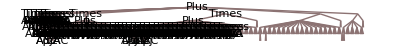

ϕ (AαiA AαiAC AβjA β2 DβjC+AαiA AαiAC AβjAC β2 Dβj+AαiA AβjA AβjAC β2 DαiC+α AαiA DαiC+2 AαiAC^2 AβjA β1 Dβj+AαiAC AαjA AβiA β4 DβjC+AαiAC AαjA AβiAC β3 Dβj+AαiAC AαjA AβjA β3 DβiC+AαiAC AαjA AβjAC β4 Dβi+AαiAC AαjAC AβiA β5 Dβj+AαiAC AαjAC AβjA β5 Dβi+AαiAC AβiA AβjA β5 DαjC+AαiAC AβiA AβjAC β4 Dαj+AαiAC AβiAC AβjA β3 Dαj+2 AαiAC AβjA^2 β1 DαiC+AαiAC AβjA AβjAC β2 Dαi+α AαiAC Dαi+AαjA AβiA AβjAC β4 DαiC+AαjA AβiAC AβjA β3 DαiC+AαjAC AβiA AβjA β5 DαiC)

(AαiAC Dαi α+AαiA DαiC α+2 AαiAC AβjA^2 DαiC β1+2 AαiAC^2 AβjA Dβj β1+AαiAC AβjA AβjAC Dαi β2+AαiA AβjA AβjAC DαiC β2+AαiA AαiAC AβjAC Dβj β2+AαiA AαiAC AβjA DβjC β2+AαjA AβiAC AβjA DαiC β3+AαiAC AβiAC AβjA Dαj β3+AαiAC AαjA AβjA DβiC β3+AαiAC AαjA AβiAC Dβj β3+AαjA AβiA AβjAC DαiC β4+AαiAC AβiA AβjAC Dαj β4+AαiAC AαjA AβjAC Dβi β4+AαiAC AαjA AβiA DβjC β4+AαjAC AβiA AβjA DαiC β5+AαiAC AβiA AβjA DαjC β5+AαiAC AαjAC AβjA Dβi β5+AαiAC AαjAC AβiA Dβj β5) ϕ

```mathematica
f=fα+fβ1+fβ2+fβ3+fβ4+fβ5
fϕ=Collect[f,ϕ]
TreeForm[fϕ]
TraditionalForm[Level[fϕ,1][[7]]]
Level[fϕ,1][[7]]
```

```mathematica
Print[Style[" ϕ^0 term: ",Red,16 ]]
Level[fϕ,1][[1;;6]]
Print[Style[" ϕ^1 term: ",Red,16 ]]
Level[fϕ,1][[7]]
Print[Style[" ϕ^2 term: ",Red,16 ]]
Level[fϕ,1][[8]]
Print[Style[" ϕ^3 term: ",Red,16 ]]
Level[fϕ,1][[9]]
Print[Style[" ϕ^4 term: ",Red,16 ]]
Level[fϕ,1][[10]]
```

ϕ^0 term:

{AαiA AαiAC α,AαiAC^2 AβjA^2 β1,AαiA AαiAC AβjA AβjAC β2,AαiAC AαjA AβiAC AβjA β3,AαiAC AαjA AβiA AβjAC β4,AαiAC AαjAC AβiA AβjA β5}

ϕ^1 term:

(AαiAC Dαi α+AαiA DαiC α+2 AαiAC AβjA^2 DαiC β1+2 AαiAC^2 AβjA Dβj β1+AαiAC AβjA AβjAC Dαi β2+AαiA AβjA AβjAC DαiC β2+AαiA AαiAC AβjAC Dβj β2+AαiA AαiAC AβjA DβjC β2+AαjA AβiAC AβjA DαiC β3+AαiAC AβiAC AβjA Dαj β3+AαiAC AαjA AβjA DβiC β3+AαiAC AαjA AβiAC Dβj β3+AαjA AβiA AβjAC DαiC β4+AαiAC AβiA AβjAC Dαj β4+AαiAC AαjA AβjAC Dβi β4+AαiAC AαjA AβiA DβjC β4+AαjAC AβiA AβjA DαiC β5+AαiAC AβiA AβjA DαjC β5+AαiAC AαjAC AβjA Dβi β5+AαiAC AαjAC AβiA Dβj β5) ϕ

ϕ^2 term:

(Dαi DαiC α+AβjA^2 DαiC^2 β1+4 AαiAC AβjA DαiC Dβj β1+AαiAC^2 Dβj^2 β1+AβjA AβjAC Dαi DαiC β2+AαiAC AβjAC Dαi Dβj β2+AαiA AβjAC DαiC Dβj β2+AαiAC AβjA Dαi DβjC β2+AαiA AβjA DαiC DβjC β2+AαiA AαiAC Dβj DβjC β2+AβiAC AβjA DαiC Dαj β3+AαjA AβjA DαiC DβiC β3+AαiAC AβjA Dαj DβiC β3+AαjA AβiAC DαiC Dβj β3+AαiAC AβiAC Dαj Dβj β3+AαiAC AαjA DβiC Dβj β3+AβiA AβjAC DαiC Dαj β4+AαjA AβjAC DαiC Dβi β4+AαiAC AβjAC Dαj Dβi β4+AαjA AβiA DαiC DβjC β4+AαiAC AβiA Dαj DβjC β4+AαiAC AαjA Dβi DβjC β4+AβiA AβjA DαiC DαjC β5+AαjAC AβjA DαiC Dβi β5+AαiAC AβjA DαjC Dβi β5+AαjAC AβiA DαiC Dβj β5+AαiAC AβiA DαjC Dβj β5+AαiAC AαjAC Dβi Dβj β5) ϕ^2

ϕ^3 term:

(2 AβjA DαiC^2 Dβj β1+2 AαiAC DαiC Dβj^2 β1+AβjAC Dαi DαiC Dβj β2+AβjA Dαi DαiC DβjC β2+AαiAC Dαi Dβj DβjC β2+AαiA DαiC Dβj DβjC β2+AβjA DαiC Dαj DβiC β3+AβiAC DαiC Dαj Dβj β3+AαjA DαiC DβiC Dβj β3+AαiAC Dαj DβiC Dβj β3+AβjAC DαiC Dαj Dβi β4+AβiA DαiC Dαj DβjC β4+AαjA DαiC Dβi DβjC β4+AαiAC Dαj Dβi DβjC β4+AβjA DαiC DαjC Dβi β5+AβiA DαiC DαjC Dβj β5+AαjAC DαiC Dβi Dβj β5+AαiAC DαjC Dβi Dβj β5) ϕ^3

ϕ^4 term:

(DαiC^2 Dβj^2 β1+Dαi DαiC Dβj DβjC β2+DαiC Dαj DβiC Dβj β3+DαiC Dαj Dβi DβjC β4+DαiC DαjC Dβi Dβj β5) ϕ^4

```mathematica
f[ϕ]=
ϕ=0 ->A-phase
```

```mathematica
Clear[AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33]
AA=Δ/(√2) {{1,I,0},{0,0,0},{0,0,0}};
DD={{D11,D12,D13},{D21,D22,D23},{D31,D32,D33}};
(******************************************)
AAT=Transpose[AA];
AAC=Conjugate[AA];
AAH=ConjugateTranspose[AA];
DDT=Transpose[DD];
DDH=ConjugateTranspose[DD];
(******************************************)
Tr[AA.AAT] (* AβjA^2,β1 ϕ^2 *)
Tr[AA.DDT](* AβjA Dβj,β1 ϕ^2 *)
Simplify[Tr[AAC.DDH],Assumptions->{{Δ}∈Reals}](* AαiAC DαiC, β1 ϕ^2 *)
Simplify[Tr[AAC.AAH],Assumptions->{{Δ}∈Reals}](* AαiAC^2,β1 ϕ^2 *)
Simplify[Tr[AA.AAH],Assumptions->{{Δ}∈Reals}](* AβjA AβjAC,β2 ϕ^2*)
Simplify[Tr[AAC.DDT],Assumptions->{{Δ}∈Reals}](* AαiAC Dαi,β2 ϕ^2||AβjAC Dβj,β2 ϕ^2 *)
Simplify[Tr[AA.DDH],Assumptions->{{Δ}∈Reals}](* AαiA DαiC,β2 ϕ^2 *)
```

0

(D11 Δ)/(√2)+(ⅈ D12 Δ)/(√2)

(Δ (Conjugate[D11]-ⅈ Conjugate[D12]))/(√2)

0

Δ^2

((D11-ⅈ D12) Δ)/(√2)

(Δ (Conjugate[D11]+ⅈ Conjugate[D12]))/(√2)

```mathematica
Clear[AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33]
AA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
BB=ΔB/(√3) {{1,0,0},{0,1,0},{0,0,1}};
ϕDD=BB-AA
%//MatrixForm
Simplify[Tr[ϕDD.ConjugateTranspose[ϕDD]],Assumptions->{{ΔB,ΔA}∈Reals}]
1/□
```

{{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}

(-ΔA/(√2)+ΔB/(√3) | -(ⅈ ΔA)/(√2) | 0
0 | ΔB/(√3) | 0
0 | 0 | ΔB/(√3))

ΔA^2-√(2/3) ΔA ΔB+ΔB^2